# Kojima’s method applied to a weird two locus genetic model

### Define a weird genetic model

Okay, so we make a model where there are two loci and thus nine genotypes. we can make a model that looks somewhat normal, but actually turns out to be weird.

```mathematica
G ={{2a, 1.5*a,0},{ a,0.5,-a},{0,-a*1.5,-2a}}
```

{{2 a,1.5 a,0},{a,0.5,-a},{0,-1.5 a,-2 a}}

```mathematica
G//MatrixForm
```

(2 a | 1.5 a | 0
a | 0.5 | -a
0 | -1.5 a | -2 a)

We need to make these vectors of possible marginal genotype frequencies in order to flesh the thing out. Mathematicas TensorProduct[] function woudl allow us to generalize this to arbitrary numbers of loci. Perhaps there is an automatic way to do this.

```mathematica
PA = {p1^2, 2*p1*(1-p1),(1-p1)^2}
PB = {p2^2, 2*p2*(1-p2),(1-p2)^2}
```

{p1^2,2 (1-p1) p1,(1-p1)^2}

{p2^2,2 (1-p2) p2,(1-p2)^2}

```mathematica
mat = TensorProduct[PA,PB]*G
```

{{2 a p1^2 p2^2,3. a p1^2 (1-p2) p2,0},{2 a (1-p1) p1 p2^2,2. (1-p1) p1 (1-p2) p2,-2 a (1-p1) p1 (1-p2)^2},{0,-3. a (1-p1)^2 (1-p2) p2,-2 a (1-p1)^2 (1-p2)^2}}

This is now a matrix of the contributions of each genotypic class to the population mean. To get the populaiton mean, we have to this sum up. We can do this by using Total[] or by crossproduct with vector of ones.

```mathematica
mat //MatrixForm
```

(2 a p1^2 p2^2 | 3. a p1^2 (1-p2) p2 | 0
2 a (1-p1) p1 p2^2 | 2. (1-p1) p1 (1-p2) p2 | -2 a (1-p1) p1 (1-p2)^2
0 | -3. a (1-p1)^2 (1-p2) p2 | -2 a (1-p1)^2 (1-p2)^2)

```mathematica
vec = ConstantArray[1,3]
```

{1,1,1}

```mathematica
vec.mat.vec
```

-2 a (1-p1)^2 (1-p2)^2-2 a (1-p1) p1 (1-p2)^2-3. a (1-p1)^2 (1-p2) p2+2. (1-p1) p1 (1-p2) p2+3. a p1^2 (1-p2) p2+2 a (1-p1) p1 p2^2+2 a p1^2 p2^2

```mathematica
u[a_,p1_,p2_] = Total[G* TensorProduct[PA,PB],{1,2}]
```

-2 a (1-p1)^2 (1-p2)^2-2 a (1-p1) p1 (1-p2)^2-3. a (1-p1)^2 (1-p2) p2+2. (1-p1) p1 (1-p2) p2+3. a p1^2 (1-p2) p2+2 a (1-p1) p1 p2^2+2 a p1^2 p2^2

### Derive some variance components using Kojimas notation

### Additive variance

We have two loci, so the additive variance will involve  taking the first derivative of the populaiton mean at both loci and multiplying respectively by the heterozgyosity at that loci.

```mathematica
VA[a_,p1_,p2_] = 0.5* p1*(1-p1)*D[u[a,p1,p2],p1]^2 +  0.5*p2*(1-p2)*D[u[a,p1,p2],p2]^2
```

0.5 (1-p2) p2 (2 a (1-p1)^2 (1-p2)+2. (1-p1) p1 (1-p2)+6. a (1-p1) p1 (1-p2)+2 a p1^2 (1-p2)+2 a (1-p1)^2 p2-2. (1-p1) p1 p2+6. a (1-p1) p1 p2+2 a p1^2 p2)^2+0.5 (1-p1) p1 (1. a (1-p1) (1-p2)^2+3. a p1 (1-p2)^2+2. (1-p1) (1-p2) p2+4 a (1-p1) (1-p2) p2-2. p1 (1-p2) p2+4 a p1 (1-p2) p2+3. a (1-p1) p2^2+1. a p1 p2^2)^2

```mathematica
VA[2,0.4,0.4]
```

5.00297

```mathematica
Plot3D[VA[1,p1,p2],{p1,0,1},{p2,0,1},AxesLabel->{Subscript[p, 1],Subscript[p, 2],VA},BaseStyle->{FontSize-> 12}]
```

-Graphics3D-

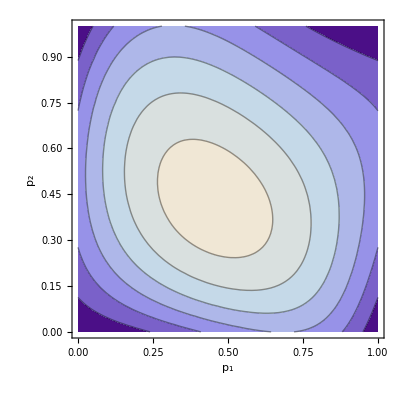

```mathematica
ContourPlot[VA[1,p1,p2],{p1,0,1},{p2,0,1},AxesLabel->{Subscript[p, 1],Subscript[p, 2],VA},BaseStyle->{FontSize-> 12}]
```

### Dominance variance

Wow, that additive variance looks strange huh! But, if you change the original model to a more basic form, you will see that it is correct. Now we do the dominance.

```mathematica
VD[a_,p1_,p2_] = 0.25* ((p1*(1-p1))^2)*D[u[a,p1,p2],{p1,2}]^2 +  0.25* ((p2*(1-p2))^2)*D[u[a,p1,p2],{p2,2}]^2
```

0.25 (0.-4. (1-p1) p1)^2 (1-p2)^2 p2^2+0.25 (1-p1)^2 p1^2 (0.+2. a (1-p2)^2-4. (1-p2) p2-2. a p2^2)^2

```mathematica
PercVA[a_,p1_,p2_]:= VA[a,p1,p2]/(VA[a,p1,p2] + VD[a,p1,p2])
VAVD[a_,p1_,p2_]:= VA[a,p1,p2] + VD[a,p1,p2]
```

```mathematica
Plot3D[VD[1,p1,p2],{p1,0,1},{p2,0,1},AxesLabel->{Subscript[p, 1],Subscript[p, 2],VD},BaseStyle->{FontSize-> 12}]
```

-Graphics3D-

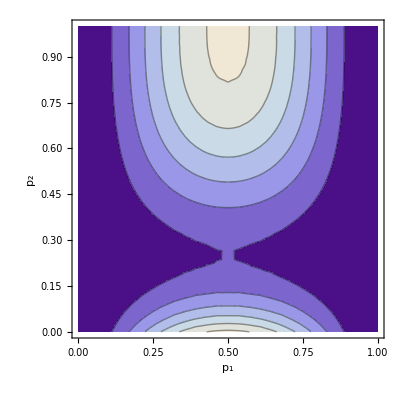

```mathematica
ContourPlot[VD[1,p1,p2],{p1,0,1},{p2,0,1},AxesLabel->{Subscript[p, 1],Subscript[p, 2],VAA},BaseStyle->{FontSize-> 12}]
```

### Additive by additive epistatic variance

```mathematica
VAA[a_,p1_,p2_] =  0.25*(p1*(1-p1))*(p2*(1-p2))*D[u[a,p1,p2],p1,p2]^2
```

0.25 (1-p1) p1 (1-p2) p2 (2. (1-p1) (1-p2)+2. a (1-p1) (1-p2)-2. p1 (1-p2)-2. a p1 (1-p2)-2. (1-p1) p2+2. a (1-p1) p2+2. p1 p2-2. a p1 p2)^2

```mathematica
Plot3D[VAA[1,p1,p2],{p1,0,1},{p2,0,1},AxesLabel->{Subscript[p, 1],Subscript[p, 2],VAA},BaseStyle->{FontSize-> 12}]
```

-Graphics3D-

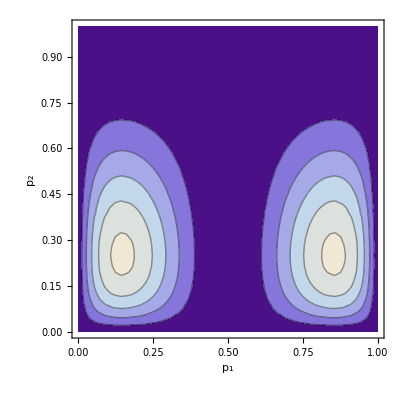

```mathematica
ContourPlot[VAA[1,p1,p2],{p1,0,1},{p2,0,1},AxesLabel->{Subscript[p, 1],Subscript[p, 2],VAA},BaseStyle->{FontSize-> 12}]
```

### Narrow sense heritability, aka the percent of total variance that is due to additive variance

```mathematica
PercVA[a_,p1_,p2_] := VA[a,p1,p2]/(VA[a,p1,p2] +VD[a,p1,p2] + VAA[a,p1,p2])
```

```mathematica
PercVA[a,p1,p2]
```

(0.5 (1-p2) p2 (2 a (1-p1)^2 (1-p2)+2. (1-p1) p1 (1-p2)+6. a (1-p1) p1 (1-p2)+2 a p1^2 (1-p2)+2 a (1-p1)^2 p2-2. (1-p1) p1 p2+6. a (1-p1) p1 p2+2 a p1^2 p2)^2+0.5 (1-p1) p1 (1. a (1-p1) (1-p2)^2+3. a p1 (1-p2)^2+2. (1-p1) (1-p2) p2+4 a (1-p1) (1-p2) p2-2. p1 (1-p2) p2+4 a p1 (1-p2) p2+3. a (1-p1) p2^2+1. a p1 p2^2)^2)/(0.25 (0.-4. (1-p1) p1)^2 (1-p2)^2 p2^2+0.25 (1-p1) p1 (1-p2) p2 (2. (1-p1) (1-p2)+2. a (1-p1) (1-p2)-2. p1 (1-p2)-2. a p1 (1-p2)-2. (1-p1) p2+2. a (1-p1) p2+2. p1 p2-2. a p1 p2)^2+0.5 (1-p2) p2 (2 a (1-p1)^2 (1-p2)+2. (1-p1) p1 (1-p2)+6. a (1-p1) p1 (1-p2)+2 a p1^2 (1-p2)+2 a (1-p1)^2 p2-2. (1-p1) p1 p2+6. a (1-p1) p1 p2+2 a p1^2 p2)^2+0.25 (1-p1)^2 p1^2 (0.+2. a (1-p2)^2-4. (1-p2) p2-2. a p2^2)^2+0.5 (1-p1) p1 (1. a (1-p1) (1-p2)^2+3. a p1 (1-p2)^2+2. (1-p1) (1-p2) p2+4 a (1-p1) (1-p2) p2-2. p1 (1-p2) p2+4 a p1 (1-p2) p2+3. a (1-p1) p2^2+1. a p1 p2^2)^2)

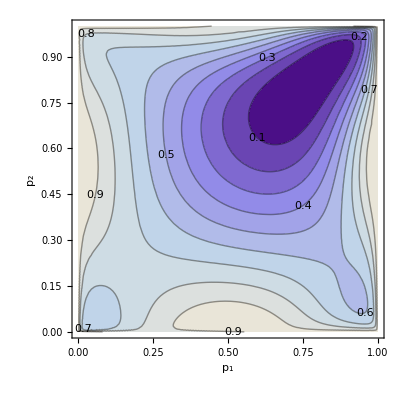

```mathematica
ContourPlot[PercVA[.1,p1,p2],{p1,0,1},{p2,0,1},FrameLabel->{Subscript[p, 1],Subscript[p, 2]},BaseStyle->{FontSize-> 12},ContourLabels->All]
```